```mathematica
(*1. Experimental parameters and geometric formulas*)
XPix=980(*number of pixels in x-direction*); 
YPix= 640(*number of pixels in x-direction*);
 d=30.3(*distance detector-sample*); 
pixx=166.6/XPix(*Pixelsize in mm in x-direction*); X0=XPix/2; Y0=YPix/2(*center position*);pixy=108.8/YPix(*Pixelsize in mm in y-direction*); korrMu=0(*Rotate whole frame by an angle korrMu in degree counter clockwise*);
mu2[X1_, Y1_]:=If[X1-X0==0, Sign[Y0-Y1]*90, 180/Pi*ArcTan[(Y0-Y1)/(X1-X0)*(pixy/pixx)]]
(*mu-conditions*)
cond1[X1_, Y1_]:=If[X1-X0<0,-1, 1]
cond2[X1_, Y1_]:=If[Y0-Y1<0,-1, 1]
(*realmu2 is mu2 in 0-360°, mu2 is only -90° to 90°*)
realmu2[X1_, Y1_]:=90*(1-cond1[X1, Y1])+90*(1+cond1[X1, Y1])*(1-cond2[X1, Y1])+mu2[X1, Y1]+korrMu
X2Y2[X1_, Y1_]:=Tan[1/2*ArcTan[1/d*Sqrt[(X1-X0)^2*(pixx)^2+(Y1-Y0)^2*(pixy)^2]]]*d
X2[X1_, Y1_]:=Cos[realmu2[X1, Y1]*Pi/180]*X2Y2[X1, Y1]
Y2[X1_, Y1_]:=Sin[realmu2[X1, Y1]*Pi/180]*X2Y2[X1, Y1]
(*Calculation of latitude gamma and longitude delta from pixel positions*)
gamma2[X1_, Y1_]:=If[Y1-Y0==0,0,ArcTan[Y2[X1, Y1]/d]*180/Pi]
delta2[X1_, Y1_]:=ArcTan[X2[X1, Y1]/Sqrt[d^2+(Y2[X1, Y1])^2]]*180/Pi
(*Goniometer hat Gamma und Delta vertauscht, d.h. der erste Kreis ist Horizontal, der zweite Vertikal. Delta zuerst, dann gamma mit geändertem Radius*)
deltaGonio[X1_, Y1_]:=If[X1-X0==0,0,ArcTan[X2[X1, Y1]/d]*180/Pi]
gammaGonio[X1_, Y1_]:=ArcTan[Y2[X1, Y1]/Sqrt[d^2+(X2[X1, Y1])^2]]*180/Pi
(*Stereographic projection of x,y,z values of gamma2, delta2 coordinates on a plane with z=1*)
proX[gamma2_, delta2_]:=2*Sin[delta2*Pi/180]*Cos[gamma2*Pi/180]/(Cos[gamma2*Pi/180]*Cos[delta2*Pi/180]+1)
proY[gamma2_, delta2_]:=2*Sin[gamma2*Pi/180]/(Cos[gamma2*Pi/180]*Cos[delta2*Pi/180]+1)
proZ[gamma2_, delta2_]:=1
(*Coordinate System: 0-point in center of image (X0, Y0) --> (0, 0). Positive x-axis to the right, positive y- axis up. realmu2 from 0° to 360° 0° is positive x-axis. Counter clockwise. Note: 0-point of Laue images (tif or png) is the upper left corner, not the center of the image.*)
Folder = "C:\\Users\\PSL Camera\\Desktop\\LV\\Part 2\\";
```

```mathematica
(*2a. Image analysis*)
Fname="LV_Probe2_300s_x2_154deg.png";
clkpts = {};
CPane=ClickPane[Import[StringJoin[Folder,Fname]],AppendTo[clkpts,#] &]
```

-Graphics-

```mathematica
LstFmt[lst_]:=StringJoin[ToString[First[lst]],"\t",ToString[Last[lst]]];
fnlpts = Map[LstFmt,clkpts];
Export[StringJoin[Folder,"LV_Pts_List_154deg.txt"],fnlpts];
```

```mathematica
(*2. List processing*)
(*Import data list with pixel x-value [TAB] y-value of diffraction spots. Other values like (hkl) can be added after additional [TAB].*)
```

```mathematica
DataPixelXY=Take[Import[StringJoin[Folder,"LV_Pts_List_154deg.txt"], "Table"], All, 2];
(*Export coordinates as longitude (gamma), latitude (delta) list*)
Export[StringJoin[Folder,"LV_Pts_List_154deg_Stereo.txt"],Transpose[{N[Apply[gamma2,DataPixelXY, {1}]], N[Apply[delta2, DataPixelXY, {1}]]}]];
```

```mathematica
DataMat={ReadList[StringJoin[Folder,"LV_Pts_List_74deg_Stereo.txt"]],ReadList[StringJoin[Folder,"LV_Pts_List_94deg_Stereo.txt"]],ReadList[StringJoin[Folder,"LV_Pts_List_114deg_Stereo.txt"]],ReadList[StringJoin[Folder,"LV_Pts_List_134deg_Stereo.txt"]],ReadList[StringJoin[Folder,"LV_Pts_List_154deg_Stereo.txt"]]};
FinalDat:=First[DataMat];
ApndDat[numb_]:=FinalDat=Join[FinalDat-Table[Last[FinalDat]-First[DataMat[[numb]]],{Length[FinalDat]}],DataMat[[numb]]];
For[i=1,i<5,i++,ApndDat[i]];
Export[StringJoin[Folder,"LV_Pts_List_All_Stereo.txt"],FinalDat];
```

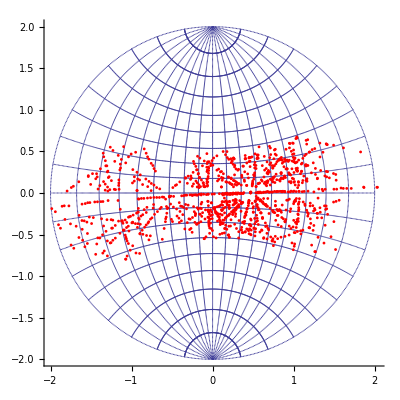

```mathematica
(*3. Stereographic projection plot*)
(*angles gamma delta that should be in the plot center*) gammaCent=0; deltaCent=-60;
(*Import list of longitude (gamma), latitude (delta) of diffraction spots*)
DataGammaDelta=ReadList[StringJoin[Folder,"LV_Pts_List_All_Stereo.txt"]]-Table[{gammaCent, deltaCent}, {Length[ReadList[StringJoin[Folder,"LV_Pts_List_All_Stereo.txt"]]]}];
(*Export gamma, delta values in stereographic projection form*)
Export[StringJoin[Folder,"LV_Pts_List_All_Stereo_shifted.txt"],Transpose[{N[Apply[proX, DataGammaDelta, {1}]], N[Apply[proY, DataGammaDelta, {1}]]}]];
(*DataSpotsProjected=ReadList[StringJoin[Folder,"example3.txt"]];*)
DataSpotsProjected=ReadList[StringJoin[Folder,"LV_Pts_List_All_Stereo_shifted.txt"]];
(*Import Wulfs Net, directory must not be changed*)
DataWulf=ReadList[StringJoin[Folder,"LGradeBGrade.txt"], Number, RecordLists->True];
(*Show graphic*)
Show[ListPlot[DataWulf,AspectRatio->1, PlotStyle->PointSize[0.002], PlotRange->{-2, 2}],ListPlot[DataSpotsProjected,AspectRatio->1, PlotStyle->{PointSize[0.005], Red}]]
```